```mathematica
Clear["Global`*"]
```

```mathematica
(* Probabilities that the donor is good given observations. Oij is the probability that the donor is good given the observation of a recipient doing action i={c,d}={cooperate,defect} to a recipient with reputation j={g,b}={good,bad}. Specifically, Ocg=P(good|->G), Ocb=P(good|->B), Odg=P(good|¬->G), and Odb=P(good|¬->B). *)
r=3;
e1=0.1;
e2=0.1;
ϵ=(1-e1)*(1-e2)+e1*e2;
e=e2;
z=0.99
g=(1-z)*gy+z*gz;
Ocg=ϵ*g/(ϵ*g+e*(1-g));
Ocb=1;
Odg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Odb=1;
```

0.99

```mathematica
(* Probabilities that a donor is good given their intention. Iij is the probability that the donor is good given their intention i={c,d}={cooperate,defect} to a recipient with reputation j={g,b}={good,bad}. *)
Icg= ϵ*Ocg + (1-ϵ)*Odg;
Icb= 1;
Idg= (1-e)*Odg + e*Ocg;
Idb= 1;
```

```mathematica
(* Changes in reputations for gx, gy, and gz *)
g2=(1-z)*gy^2+z*gz^2;
gyplus=(1-gy)*(Idg*g+1-g);
gyminus=gy*(1-Idg)*g;
gy2plus=(gy-gy2)*(Idg*g+1-g);
gy2minus=gy2*(1-Idg)*g;
gzplus=(1-gz)*(Icg*g2+(g-g2)*Idg +1-g);
gzminus=gz*((1-Icg)*g2+(g-g2)*(1-Idg));
gz2plus=(gz-gz2)*(Icg*g2+(g-g2)*Idg +1-g);
gz2minus=gz2*((1-Icg)*g2+(g-g2)*(1-Idg));
sol =Solve[gyplus==gyminus&&gy2plus==gy2minus&&gzplus==gzminus&&gz2plus==gz2minus&&0≤ gy≤ 1&&0≤ gy2≤ 1&&0≤ gz≤ 1&&0≤ gz2≤ 1,{gy,gy2,gz,gz2},Reals]
(*{{Gx,Gy,Gz}}=Values[Solve[gxplus==gxminus&&gyplus==gyminus&&gzplus==gzminus,{gx,gy,gz}]]/.{x->x[t],y->y[t],z->z[t]}*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{gy→0.88513,gy2→0.783454,gz→0.971578,gz2→0.943964},{gy→1.,gy2→1.,gz→1.,gz2→1.}}

```mathematica
(* The replicator equations *)
Py=r*z*gy/.sol;
Pz=r*z*gz-(1-z)*gy-z*gz/.sol;
Pbar=(1-z[t])*Py+z*Pz/.sol;
zdot=z*(1-z)*(Pz-Py)/.sol;
Pz-Py
```

{-0.713962,-1.}

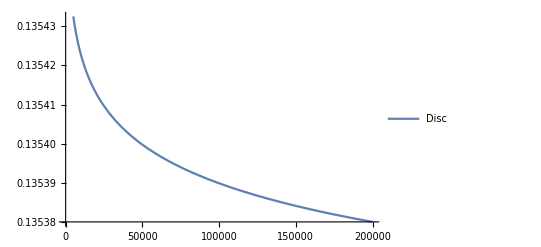

```mathematica
(* Plot numerical solutions *)
params={τ-> 100,r->3,ϵ->(1-e1)*(1-e2)+e1*e2,e->e2,e1->0.01,e2->0.01};
eqns={z'[t]==zdot,gy'[t]==τ*Δgy,gz'[t]==τ*Δgz}//.params;
z0=RandomReal[];
gy0=RandomReal[];
gz0=RandomReal[];
IC={z[0]==z0,gy[0]==gy0,gz[0]== gz0};
sol=NDSolve[Join[eqns,IC],{z,gy,gz},{t,0,200000}];
Plot[Evaluate[{z[t]}/.sol],{t,0,200000},PlotLegends->{"Disc"}]
```

```mathematica
nsoleq={0==xdot,0==ydot,0==zdot,0==Δgx,0==Δgy,0==Δgz};
conds={0≤ x≤ 1,0≤y≤ 1,0≤z≤ 1,x+y+z==1,0≤gx≤ 1,0≤gy≤ 1,0≤gz≤ 1}
nsol=NSolve[Join[nsoleq,conds]/.{x[t]->x,y[t]->y,z[t]->z,gx[t]->gx,gy[t]->gy,gz[t]->gz},{x,y,z,gx,gy,gz},Reals]
```

{0≤x≤1,0≤y≤1,0≤z≤1,x+y+z==1,0≤gx≤1,0≤gy≤1,0≤gz≤1}

$Aborted